```mathematica
μ = Quantity[100,"Kilograms"]
```

100 kg

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[R, e]]
```

```mathematica
Subscript[R, e]= Quantity[6378.1*^3,"Meters"]
```

6.3781×10^6 m

```mathematica
3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[R, 0]]
```

```mathematica
Subscript[R, 0] = 3*Subscript[R, e]
```

1.91343×10^7 m

```mathematica
Symbolize[Subscript[M, e]]
```

```mathematica
Subscript[M, e] = Quantity[5.972*^24 , "Kilograms"]
```

5.972×10^24 kg

```mathematica
G= UnitConvert[Quantity[1,"GravitationalConstant"]]
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Symbolize[Subscript[l, scale]]
```

```mathematica
Subscript[l, scale] = 0.5
```

0.5

```mathematica
l = μ*Subscript[R, 0] * Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

4.36656×10^12 kg m^2/s

```mathematica
Symbolize[Subscript[v, r,0]]
```

```mathematica
Symbolize[Subscript[v, t,0]]
```

```mathematica
Subscript[v, r,0] = Quantity[500,"Meters"/"Seconds"]
```

500 m/s

```mathematica
Subscript[v, t,0] = Sqrt[G*Subscript[M, e]/Subscript[R, 0]]*Subscript[l, scale]
```

2282.06 m/s

```mathematica
Symbolize[Subscript[E, t]]
```

```mathematica
Subscript[E, t] = (1/2)*μ*(Subscript[v, t,0]^2 + Subscript[v, r,0]^2) - G*Subscript[M, e]*μ/Subscript[R, 0]
```

-1.81022×10^9 kg m^2/s^2

```mathematica
Subscript[E, t] + G*Subscript[M, e]*μ/Subscript[R, 0] - l^2/(2*μ*Subscript[R, 0]^2)
```

1.25×10^7 kg m^2/s^2

```mathematica
r = Quantity["Meters"]
```

1 m

```mathematica
f[r_]:= Subscript[R, 0]*(l/r^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/r - l^2/(2*μ*r^2))]
```

```mathematica
f[Subscript[R, 0]]
```

4.56411

```mathematica
Subscript[R, 0]
```

1.91343×10^7 m

```mathematica
g[x_]:= Subscript[R, 0]*(l/Quantity[x,"Meters"]^2)/Sqrt[2*μ*(Subscript[E, t] + G*Subscript[M, e]*μ/Quantity[x,"Meters"] - l^2/(2*μ*Quantity[x,"Meters"]^2))]
```

```mathematica
g[8*^9]
```

0.-2.17264×10^-6 ⅈ

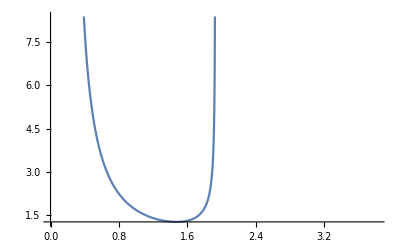

```mathematica
Plot[g[x],{x,0*QuantityMagnitude@Subscript[R, 0],2*QuantityMagnitude@Subscript[R, 0]}]
```

```mathematica
d[x_]:=(-1/Subscript[E, t])*(Subscript[E, t] + G*Subscript[M, e]*μ/Quantity[x,"Meters"] - l^2/(2*μ*Quantity[x,"Meters"]^2))
```

```mathematica
d[1*QuantityMagnitude@Subscript[R, 0]]
```

0.00690522

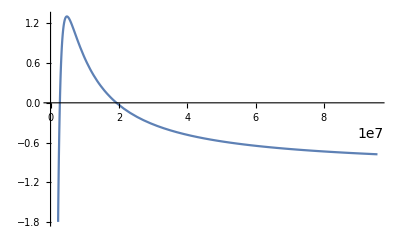

```mathematica
Plot[d[x],{x,0*QuantityMagnitude@Subscript[R, 0],5*QuantityMagnitude@Subscript[R, 0]}]
```

```mathematica
r1=Quantity[FindRoot[d,{0.001*QuantityMagnitude@Subscript[R, 0],1*QuantityMagnitude@Subscript[R, 0]}],"Meters"]/Subscript[R, 0]
```

{0.142694}

```mathematica
r2=Quantity[FindRoot[d,{2*QuantityMagnitude@Subscript[R, 0],5*QuantityMagnitude@Subscript[R, 0]}],"Meters"]/Subscript[R, 0]
```

{1.00805}

```mathematica
θ[r_]:= Integrate[g[x]/(QuantityMagnitude@Subscript[R, 0]),{x,r1*QuantityMagnitude@Subscript[R, 0],r}]
```

```mathematica
θ[1.0*QuantityMagnitude@Subscript[R, 0]]
```

3.06869

```mathematica
r2*QuantityMagnitude@Subscript[R, 0]
```

{1.92884×10^7}

```mathematica
h[r_,x_]:=θ[r]-x
```

```mathematica
R[x_]:= FindRoot[θ[Quantity[r,"Meters"]]-x,{r1*QuantityMagnitude@Subscript[R, 0],r2*QuantityMagnitude@Subscript[R, 0]}]
```

```mathematica
R[1.0]
```

Quantity::compat: 1/Meters^2 and 1/Meters^4 are incompatible units

General::stop: Further output of Quantity::compat will be suppressed during this calculation.

Less::nord2: Comparison of 1. and 2.7303548441674881615×10^6 is invalid.

GreaterEqual::nord2: Comparison of 1. and 2.7303548441674881615×10^6 is invalid.

Less::nord2: Comparison of 1. and 2.7303548441674881615×10^6 is invalid.

GreaterEqual::nord2: Comparison of 1. and 2.7303548441674881615×10^6 is invalid.

General::stop: Further output of GreaterEqual::nord2 will be suppressed during this calculation.

Less::nord2: Comparison of 1. and 2.7303548441674881615×10^6 is invalid.

General::stop: Further output of Less::nord2 will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {} {-2.73035×10^6+1.} cannot be combined.